### Сalculate the initial conditions for the first stage m'[x]==-u

```mathematica
Clear[all]
sol1=Flatten[Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==-SubStar[u],θ[0]==1,ω[0]==Subscript[Ω, 0],m[0]==0},{θ[x],ω[x],m[x]},x]]]
```

{m[x]→-x u_*,θ[x]→1/2 ⅇ^-x (1+ⅇ^(2 x)+(-1+ⅇ^(2 x)) Ω_0+(1-ⅇ^(2 x)+2 ⅇ^x x) u_*),ω[x]→1/2 ⅇ^-x ((1+ⅇ^(2 x)) Ω_0-(-1+ⅇ^x) (-1-ⅇ^x+(-1+ⅇ^x) u_*))}

```mathematica
initForStage2={m[x]/.sol1⟦1⟧/.x->Subscript[τ, 1],θ[x]/.sol1⟦2⟧/.x->Subscript[τ, 1],ω[x]/.sol1⟦3⟧/.x->Subscript[τ, 1]}
```

{-τ_1 u_*,1/2 ⅇ^-τ_1 (1+ⅇ^(2 τ_1)+(-1+ⅇ^(2 τ_1)) Ω_0+(1-ⅇ^(2 τ_1)+2 ⅇ^τ_1 τ_1) u_*),1/2 ⅇ^-τ_1 ((1+ⅇ^(2 τ_1)) Ω_0-(-1+ⅇ^τ_1) (-1-ⅇ^τ_1+(-1+ⅇ^τ_1) u_*))}

### Сalculate the initial conditions for the second stage m'[x]==u

```mathematica
sol2=Flatten[Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==SubStar[u],θ[Subscript[τ, 1]]==initForStage2[[2]],ω[Subscript[τ, 1]]==initForStage2[[3]],m[Subscript[τ, 1]]==initForStage2[[1]]},{θ[x],ω[x],m[x]},x]]]
```

{m[x]→(x-2 τ_1) u_*,θ[x]→1/2 (ⅇ^-x+ⅇ^x+(-ⅇ^-x+ⅇ^x) Ω_0+(ⅇ^-x-ⅇ^x+2 ⅇ^(x-τ_1)-2 ⅇ^(-x+τ_1)-2 x+4 τ_1) u_*),ω[x]→1/2 ⅇ^(-x-τ_1) (ⅇ^τ_1 (-1+ⅇ^(2 x))+ⅇ^τ_1 (1+ⅇ^(2 x)) Ω_0-(-2 ⅇ^(2 x)+ⅇ^τ_1-2 ⅇ^(2 τ_1)+2 ⅇ^(x+τ_1)+ⅇ^(2 x+τ_1)) u_*)}

### Сalculate the initial conditions for the third stage m'[x]==-u

```mathematica
sol3=Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==-SubStar[u],θ[Subscript[τ, f]]==0,ω[Subscript[τ, f]]==0,m[Subscript[τ, f]]==0},{θ[x],ω[x],m[x]},x]]//Flatten
```

{m[x]→(-x+τ_f) u_*,θ[x]→1/2 (-ⅇ^(x-τ_f)+ⅇ^(-x+τ_f)+2 x-2 τ_f) u_*,ω[x]→-1/2 ⅇ^(-x-τ_f) (ⅇ^x-ⅇ^τ_f)^2 u_*}

```mathematica
linkingStage2={m[x]/.sol2⟦1⟧/.x->Subscript[τ, 2],θ[x]/.sol2⟦2⟧/.x->Subscript[τ, 2]//Simplify,ω[x]/.sol2⟦3⟧/.x->Subscript[τ, 2]//Simplify}
```

{(-2 τ_1+τ_2) u_*,1/2 (ⅇ^-τ_2+ⅇ^τ_2+(-ⅇ^-τ_2+ⅇ^τ_2) Ω_0+(-2 ⅇ^(τ_1-τ_2)+ⅇ^-τ_2-ⅇ^τ_2+2 ⅇ^(-τ_1+τ_2)+4 τ_1-2 τ_2) u_*),1/2 ⅇ^(-τ_1-τ_2) (ⅇ^τ_1 (-1+ⅇ^(2 τ_2))+ⅇ^τ_1 (1+ⅇ^(2 τ_2)) Ω_0-(ⅇ^τ_1-2 ⅇ^(2 τ_1)-2 ⅇ^(2 τ_2)+2 ⅇ^(τ_1+τ_2)+ⅇ^(τ_1+2 τ_2)) u_*)}

```mathematica
linkingStage3={m[x]/.sol3⟦1⟧/.x->Subscript[τ, 2],θ[x]/.sol3⟦2⟧/.x->Subscript[τ, 2]//Simplify,ω[x]/.sol3⟦3⟧/.x->Subscript[τ, 2]//Simplify}
```

{(-τ_2+τ_f) u_*,1/2 (-ⅇ^(τ_2-τ_f)+ⅇ^(-τ_2+τ_f)+2 τ_2-2 τ_f) u_*,-1/2 ⅇ^(-τ_2-τ_f) (ⅇ^τ_2-ⅇ^τ_f)^2 u_*}

```mathematica
first=(linkingStage2[[1]]-linkingStage3[[1]]==0//Simplify)
```

(2 τ_1-2 τ_2+τ_f) u_*==0

```mathematica
first1=z==y/x
```

z==y/x

```mathematica
second=(linkingStage2[[2]]-linkingStage3[[2]]==0//Simplify)
```

1/2 (ⅇ^-τ_2+ⅇ^τ_2+(-ⅇ^-τ_2+ⅇ^τ_2) Ω_0+(-2 ⅇ^(τ_1-τ_2)+ⅇ^-τ_2-ⅇ^τ_2+2 ⅇ^(-τ_1+τ_2)+ⅇ^(τ_2-τ_f)-ⅇ^(-τ_2+τ_f)+4 τ_1-4 τ_2+2 τ_f) u_*)==0

```mathematica
second1=1/2 (1/y+y+(-1/y+y) Subscript[Ω, 0]+((-2x)/y+1/y-y+(2y)/x+(y*x^2)/y^2-y^2/(x^2 y)) SubStar[u])==0
```

1/2 (1/y+y+(-1/y+y) Ω_0+(1/y-(2 x)/y+x^2/y-y-y/x^2+(2 y)/x) u_*)==0

```mathematica
third=(linkingStage2[[3]]-linkingStage3[[3]]==0//Simplify)
```

1/2 ⅇ^-τ_2 (-1+ⅇ^(2 τ_2)+(1+ⅇ^(2 τ_2)) Ω_0+(-1+2 ⅇ^τ_1-4 ⅇ^τ_2-ⅇ^(2 τ_2)+2 ⅇ^(-τ_1+2 τ_2)+ⅇ^(2 τ_2-τ_f)+ⅇ^τ_f) u_*)==0

```mathematica
third1=1/2  1/y(-1+y^2+(1+y^2) Subscript[Ω, 0]+(-1+2 x-4 y-y^2+2 y^2/x+(y^2 x^2)/y^2+y^2/x^2) SubStar[u])==0
```

(-1+y^2+(1+y^2) Ω_0+(-1+2 x+x^2-4 y-y^2+y^2/x^2+(2 y^2)/x) u_*)/(2 y)==0

```mathematica
SubStar[t]=0.346; Subscript[ω, 0]=0.069;Subscript[ϕ, 0]=0.087;SubStar[u]=1.65;Subscript[Ω, 0]=SubStar[t]/Subscript[ϕ, 0] Subscript[ω, 0];Subscript[Ω, 0base]=Subscript[Ω, 0];
Print["Ω_0=",Subscript[Ω, 0]];
```

Ω_0=0.274414

```mathematica
Subscript[Ω, 0]=Subscript[Ω, 0base];(*roots=FindRoot[{first,second,third},{Subscript[τ, 1],0.2},{Subscript[τ, 2],1},{Subscript[τ, f],3},MaxIterations->Infinity]*)
roots=NSolve[third1&&second1&&first1,{x,y,z},Reals]
```

{{x→8.37734,y→132.231,z→15.7844},{x→-0.465476,y→-0.532064,z→1.14305}}

```mathematica
Subscript[τ, 1]=Log[roots[[1]][[1]][[2]]];Subscript[τ, 2]=Log[roots[[1]][[2]][[2]]];Subscript[τ, f]=2*Log[roots[[1]][[3]][[2]]];
Print["τ1=",Subscript[τ, 1],"; τ2=",Subscript[τ, 2],"; τf=",Subscript[τ, f]]
```

τ1=2.12553; τ2=4.88455; τf=5.51805

```mathematica
Subscript[τ, 1]=Log[roots[[1]][[1]][[2]]];Subscript[τ, 2]=Log[roots[[1]][[2]][[2]]]; Subscript[τ, f]=2*Log[roots[[1]][[3]][[2]]];
pw1m=Piecewise[{{sol1[[1]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[1]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[1]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}];
pw1θ=Piecewise[{{sol1[[2]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[2]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[2]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}]
pw1ω=Piecewise[{{sol1[[3]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[3]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[3]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}]
```

Piecewise[{{1/2 ⅇ^-x (1+ⅇ^(2 x)+0.274414 (-1+ⅇ^(2 x))+1.65 (1-ⅇ^(2 x)+2 ⅇ^x x)), x>0&&x≤2.12553}, {1/2 (ⅇ^-x+ⅇ^x+0.274414 (-ⅇ^-x+ⅇ^x)+1.65 (8.50212-2 ⅇ^(2.12553-x)+2 ⅇ^(-2.12553+x)+ⅇ^-x-ⅇ^x-2 x)), x>2.12553&&x≤4.88455}, {0.825 (-11.0361+ⅇ^(5.51805-x)-ⅇ^(-5.51805+x)+2 x), x>4.88455&&x≤5.51805}, {0, True}}]

Piecewise[{{1/2 ⅇ^-x (0.274414 (1+ⅇ^(2 x))-(-1+ⅇ^x) (-1-ⅇ^x+1.65 (-1+ⅇ^x))), x>0&&x≤2.12553}, {1/2 ⅇ^(-2.12553-x) (8.37734 (-1+ⅇ^(2 x))+2.29886 (1+ⅇ^(2 x))-1.65 (-131.982-2 ⅇ^(2 x)+2 ⅇ^(2.12553+x)+ⅇ^(2.12553+2 x))), x>2.12553&&x≤4.88455}, {-0.825 ⅇ^(-5.51805-x) (-249.148+ⅇ^x)^2, x>4.88455&&x≤5.51805}, {0, True}}]

```mathematica
Subscript[Ω, 0]=1.3 Subscript[Ω, 0base]; roots=NSolve[third1&&second1&&first1,{x,y,z},Reals]
Subscript[τ, 1]=Log[roots[[1]][[1]][[2]]];Subscript[τ, 2]=Log[roots[[1]][[2]][[2]]]; Subscript[τ, f]=2*Log[roots[[1]][[3]][[2]]];
pw13m=Piecewise[{{sol1[[1]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[1]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[1]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}];
pw13θ=Piecewise[{{sol1[[2]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[2]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[2]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}]
pw13ω=Piecewise[{{sol1[[3]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[3]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[3]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}]
```

{{x→10.8519,y→224.891,z→20.7236},{x→-0.392483,y→-0.444911,z→1.13358}}

Piecewise[{{1/2 ⅇ^-x (1+ⅇ^(2 x)+0.356738 (-1+ⅇ^(2 x))+1.65 (1-ⅇ^(2 x)+2 ⅇ^x x)), x>0&&x≤2.38434}, {1/2 (ⅇ^-x+ⅇ^x+0.356738 (-ⅇ^-x+ⅇ^x)+1.65 (9.53736-2 ⅇ^(2.38434-x)+2 ⅇ^(-2.38434+x)+ⅇ^-x-ⅇ^x-2 x)), x>2.38434&&x≤5.41561}, {0.825 (-12.1251+ⅇ^(6.06255-x)-ⅇ^(-6.06255+x)+2 x), x>5.41561&&x≤6.06255}, {0, True}}]

Piecewise[{{1/2 ⅇ^-x (0.356738 (1+ⅇ^(2 x))-(-1+ⅇ^x) (-1-ⅇ^x+1.65 (-1+ⅇ^x))), x>0&&x≤2.38434}, {1/2 ⅇ^(-2.38434-x) (10.8519 (-1+ⅇ^(2 x))+3.87129 (1+ⅇ^(2 x))-1.65 (-224.676-2 ⅇ^(2 x)+2 ⅇ^(2.38434+x)+ⅇ^(2.38434+2 x))), x>2.38434&&x≤5.41561}, {-0.825 ⅇ^(-6.06255-x) (-429.467+ⅇ^x)^2, x>5.41561&&x≤6.06255}, {0, True}}]

```mathematica
Subscript[Ω, 0]=0.7 Subscript[Ω, 0base]; roots=NSolve[third1&&second1&&first1,{x,y,z},Reals]
Subscript[τ, 1]=Log[roots[[1]][[1]][[2]]];Subscript[τ, 2]=Log[roots[[1]][[2]][[2]]]; Subscript[τ, f]=2*Log[roots[[1]][[3]][[2]]];
pw07m=Piecewise[{{sol1[[1]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[1]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[1]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}];
pw07θ=Piecewise[{{sol1[[2]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[2]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[2]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}]
pw07ω=Piecewise[{{sol1[[3]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[3]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, 2]},{sol3[[3]][[2]],x>Subscript[τ, 2]&&x<=Subscript[τ, f]}}]
```

{{x→7.83272,y→115.13,z→14.6986},{x→-0.489234,y→-0.560445,z→1.14556}}

Piecewise[{{1/2 ⅇ^-x (1+ⅇ^(2 x)+0.249717 (-1+ⅇ^(2 x))+1.65 (1-ⅇ^(2 x)+2 ⅇ^x x)), x>0&&x≤2.05831}, {1/2 (ⅇ^-x+ⅇ^x+0.249717 (-ⅇ^-x+ⅇ^x)+1.65 (8.23324-2 ⅇ^(2.05831-x)+2 ⅇ^(-2.05831+x)+ⅇ^-x-ⅇ^x-2 x)), x>2.05831&&x≤4.74606}, {0.825 (-10.751+ⅇ^(5.37551-x)-ⅇ^(-5.37551+x)+2 x), x>4.74606&&x≤5.37551}, {0, True}}]

Piecewise[{{1/2 ⅇ^-x (0.249717 (1+ⅇ^(2 x))-(-1+ⅇ^x) (-1-ⅇ^x+1.65 (-1+ⅇ^x))), x>0&&x≤2.05831}, {1/2 ⅇ^(-2.05831-x) (7.83272 (-1+ⅇ^(2 x))+1.95596 (1+ⅇ^(2 x))-1.65 (-114.87-2 ⅇ^(2 x)+2 ⅇ^(2.05831+x)+ⅇ^(2.05831+2 x))), x>2.05831&&x≤4.74606}, {-0.825 ⅇ^(-5.37551-x) (-216.05+ⅇ^x)^2, x>4.74606&&x≤5.37551}, {0, True}}]

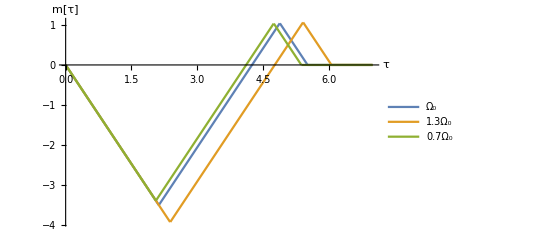

```mathematica
Plot[{pw1m,pw13m,pw07m},{x,0,7},AxesLabel->{Style["τ",17,Black],Style["m[τ]",17,Black]},PlotLegends->{"Ω_0","1.3Ω_0","0.7Ω_0"}]
```

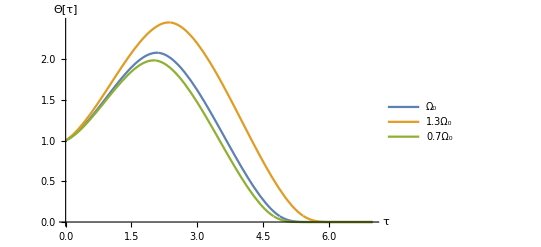

```mathematica
Plot[{pw1θ,pw13θ,pw07θ},{x,0,7},AxesLabel->{Style["τ",17,Black],Style["Θ[τ]",17,Black]},PlotLegends->{"Ω_0","1.3Ω_0","0.7Ω_0"}]
```

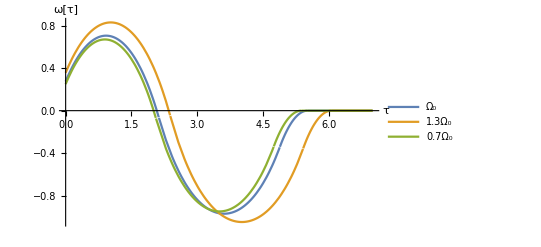

```mathematica
Plot[{pw1ω,pw13ω,pw07ω},{x,0,7},AxesLabel->{Style["τ",17,Black],Style["ω[τ]",17,Black]},PlotLegends->{"Ω_0","1.3Ω_0","0.7Ω_0"}]
```